```mathematica
x
```

x



```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
FullSimplify[ArcCurvature[{x,(x^3-x)/x^a},x],x∈Reals∧a∈]
```

√((x^(-2+4 a) ((-1+a) a-(-3+a) (-2+a) x^2)^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3))

```mathematica
PowerExpand[√((x^(-2+4 a) ((-1+a) a-(-3+a) (-2+a) x^2)^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3))]
```

(x^(1/2 (-2+4 a)) ((-1+a) a-(-3+a) (-2+a) x^2))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))

```mathematica
ApartSquareFree[(x^(1/2 (-2+4 a)) ((-1+a) a-(-3+a) (-2+a) x^2))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2)),x]
```

-(a x^(-1+2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))+(a^2 x^(-1+2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))-(6 x^(1+2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))+(5 a x^(1+2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))-(a^2 x^(1+2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))

```mathematica
ArgMax[√((x^(-2+4 a) ((-1+a) a-(-3+a) (-2+a) x^2)^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)),{x}]
```

ArgMax[√((x^(-2+4 a) ((-1+a) a-(-3+a) (-2+a) x^2)^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)),{x}]

```mathematica
Maximize[√((x^(-2+4 a) ((-1+a) a-(-3+a) (-2+a) x^2)^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)),{x}]
```

Maximize[√((x^(-2+4 a) ((-1+a) a-(-3+a) (-2+a) x^2)^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)),{x}]

```mathematica
D[-(a x^(-1+2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))+(a^2 x^(-1+2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))-(6 x^(1+2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))+(5 a x^(1+2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))-(a^2 x^(1+2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2)),x]==0
```

(3 a x^(-1+2 a) (2 a x^(-1+2 a)+4 (-3+a) x (1-a+(-3+a) x^2)))/(2 (x^(2 a)+(1-a+(-3+a) x^2)^2)^(5/2))-(3 a^2 x^(-1+2 a) (2 a x^(-1+2 a)+4 (-3+a) x (1-a+(-3+a) x^2)))/(2 (x^(2 a)+(1-a+(-3+a) x^2)^2)^(5/2))+(9 x^(1+2 a) (2 a x^(-1+2 a)+4 (-3+a) x (1-a+(-3+a) x^2)))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(5/2))-(15 a x^(1+2 a) (2 a x^(-1+2 a)+4 (-3+a) x (1-a+(-3+a) x^2)))/(2 (x^(2 a)+(1-a+(-3+a) x^2)^2)^(5/2))+(3 a^2 x^(1+2 a) (2 a x^(-1+2 a)+4 (-3+a) x (1-a+(-3+a) x^2)))/(2 (x^(2 a)+(1-a+(-3+a) x^2)^2)^(5/2))-(6 (1+2 a) x^(2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))+(5 a (1+2 a) x^(2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))-(a^2 (1+2 a) x^(2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))-(a (-1+2 a) x^(-2+2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))+(a^2 (-1+2 a) x^(-2+2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))==0

```mathematica
FullSimplify[D[-(a x^(-1+2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))+(a^2 x^(-1+2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))-(6 x^(1+2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))+(5 a x^(1+2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2))-(a^2 x^(1+2 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^(3/2)),x]==0,x∈Reals∧a∈]
```

(x^(-1+a) (-2 a^5 (-1+x^2)^3+a^4 (-1+x^2)^2 (-7+27 x^2)+6 x^2 (-1-12 x^2+45 x^4-x^(2 a))+a^3 (-1+x^2) (-9+86 x^2-145 x^4+x^(2 a))+a (1-19 x^2+291 x^4-513 x^6+x^(2 a) (1+11 x^2))+a^2 (-5+x^2 (85-395 x^2+387 x^4-6 x^(2 a)))))/(√(x^(2 a)+(1-a+(-3+a) x^2)^2))==0

```mathematica
Solve[
(x^(-1+a) (-2 a^5 (-1+x^2)^3+a^4 (-1+x^2)^2 (-7+27 x^2)+6 x^2 (-1-12 x^2+45 x^4-x^(2 a))+a^3 (-1+x^2) (-9+86 x^2-145 x^4+x^(2 a))+a (1-19 x^2+291 x^4-513 x^6+x^(2 a) (1+11 x^2))+a^2 (-5+x^2 (85-395 x^2+387 x^4-6 x^(2 a)))))/(√(x^(2 a)+(1-a+(-3+a) x^2)^2))==0,a,]
```

Solve::nsmet: This system cannot be solved with the methods available to Solve.

Solve[(x^(-1+a) (-2 a^5 (-1+x^2)^3+a^4 (-1+x^2)^2 (-7+27 x^2)+6 x^2 (-1-12 x^2+45 x^4-x^(2 a))+a^3 (-1+x^2) (-9+86 x^2-145 x^4+x^(2 a))+a (1-19 x^2+291 x^4-513 x^6+x^(2 a) (1+11 x^2))+a^2 (-5+x^2 (85-395 x^2+387 x^4-6 x^(2 a)))))/(√(x^(2 a)+(1-a+(-3+a) x^2)^2))==0,a,]

```mathematica
FunctionDomain[x/(x^4-1),x]
```

x<-1||-1<x<1||x>1

```mathematica
FunctionDomain[√x,x]
```

x≥0

```mathematica
FunctionDomain[Log[x],x]
```

x>0

```mathematica
FunctionDomain[x^2,x]
```

True

```mathematica
FunctionRange[x^2,x]
```

FunctionRange::argt: FunctionRange called with 2 arguments; 3 or 4 arguments are expected.

FunctionRange[x^2,x]

```mathematica
FunctionRange[x^2,x,Reals]
```

ℝ≥0

```mathematica
FunctionRange[x^2,x,y]
```

y≥0

```mathematica
FunctionRange[x^2,x,]
```

≥0

```mathematica
Beta[x,Sqrt[x]]
```

Beta[x,√x]

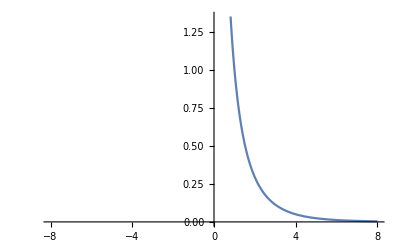

```mathematica
Plot[Beta[x,√x],{x,-8,8}]
```

```mathematica
Plot3D[√((x^(-2+4 a) ((-1+a) a-(-3+a) (-2+a) x^2)^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)),{x,a}∈Disk[{0,0},10]]
```

-Graphics3D-

```mathematica
Plot3D[√((x^(-2+4 a) ((-1+a) a-(-3+a) (-2+a) x^2)^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)),{x,a}∈Disk[{0,0},10],AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
FunctionDomain[√((x^(-2+4 a) ((-1+a) a-(-3+a) (-2+a) x^2)^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)),{x,a}]
```

(2 a∈ℤ&&4 a∈ℤ&&x≠0&&1-2 a+a^2-6 x^2+8 a x^2-2 a^2 x^2+9 x^4-6 a x^4+a^2 x^4+x^(2 a)≠0&&(12 a x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(22 a^2 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(12 a^3 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^4 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^2 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^3 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(36 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(60 a x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(37 a^2 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(10 a^3 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)≥0)||(2 a∈ℤ&&4 a∈ℤ&&1-2 a+a^2-6 x^2+8 a x^2-2 a^2 x^2+9 x^4-6 a x^4+a^2 x^4+x^(2 a)≠0&&(12 a x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(22 a^2 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(12 a^3 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^4 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^2 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^3 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(36 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(60 a x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(37 a^2 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(10 a^3 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)≥0&&a≥3/4)||(2 a∈ℤ&&x≥0&&1-2 a+a^2-6 x^2+8 a x^2-2 a^2 x^2+9 x^4-6 a x^4+a^2 x^4+x^(2 a)≠0&&(12 a x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(22 a^2 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(12 a^3 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^4 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^2 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^3 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(36 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(60 a x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(37 a^2 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(10 a^3 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)≥0&&a>1/2)||(4 a∈ℤ&&x>0&&1-2 a+a^2-6 x^2+8 a x^2-2 a^2 x^2+9 x^4-6 a x^4+a^2 x^4+x^(2 a)≠0&&(12 a x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(22 a^2 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(12 a^3 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^4 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^2 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^3 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(36 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(60 a x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(37 a^2 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(10 a^3 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)≥0&&a>0)||(4 a∈ℤ&&x≥0&&1-2 a+a^2-6 x^2+8 a x^2-2 a^2 x^2+9 x^4-6 a x^4+a^2 x^4+x^(2 a)≠0&&(12 a x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(22 a^2 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(12 a^3 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^4 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^2 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^3 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(36 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(60 a x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(37 a^2 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(10 a^3 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)≥0&&a≥3/4)||(x≥0&&1-2 a+a^2-6 x^2+8 a x^2-2 a^2 x^2+9 x^4-6 a x^4+a^2 x^4+x^(2 a)≠0&&(12 a x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(22 a^2 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(12 a^3 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^4 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^2 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^3 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(36 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(60 a x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(37 a^2 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(10 a^3 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)≥0&&a>1/2)||(x>0&&1-2 a+a^2-6 x^2+8 a x^2-2 a^2 x^2+9 x^4-6 a x^4+a^2 x^4+x^(2 a)≠0&&(12 a x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(22 a^2 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(12 a^3 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^4 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^2 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^3 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(36 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(60 a x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(37 a^2 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(10 a^3 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)≥0)

```mathematica
FunctionDomain[√((x^(-2+4 a) ((-1+a) a-(-3+a) (-2+a) x^2)^2)/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)),{x,a},Reals]
```

(2 a∈ℤ&&4 a∈ℤ&&x≠0&&1-2 a+a^2-6 x^2+8 a x^2-2 a^2 x^2+9 x^4-6 a x^4+a^2 x^4+x^(2 a)≠0&&(12 a x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(22 a^2 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(12 a^3 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^4 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^2 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^3 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(36 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(60 a x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(37 a^2 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(10 a^3 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)≥0)||(2 a∈ℤ&&4 a∈ℤ&&1-2 a+a^2-6 x^2+8 a x^2-2 a^2 x^2+9 x^4-6 a x^4+a^2 x^4+x^(2 a)≠0&&(12 a x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(22 a^2 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(12 a^3 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^4 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^2 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^3 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(36 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(60 a x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(37 a^2 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(10 a^3 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)≥0&&a≥3/4)||(2 a∈ℤ&&x≥0&&1-2 a+a^2-6 x^2+8 a x^2-2 a^2 x^2+9 x^4-6 a x^4+a^2 x^4+x^(2 a)≠0&&(12 a x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(22 a^2 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(12 a^3 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^4 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^2 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^3 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(36 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(60 a x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(37 a^2 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(10 a^3 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)≥0&&a>1/2)||(4 a∈ℤ&&x>0&&1-2 a+a^2-6 x^2+8 a x^2-2 a^2 x^2+9 x^4-6 a x^4+a^2 x^4+x^(2 a)≠0&&(12 a x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(22 a^2 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(12 a^3 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^4 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^2 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^3 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(36 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(60 a x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(37 a^2 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(10 a^3 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)≥0&&a>0)||(4 a∈ℤ&&x≥0&&1-2 a+a^2-6 x^2+8 a x^2-2 a^2 x^2+9 x^4-6 a x^4+a^2 x^4+x^(2 a)≠0&&(12 a x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(22 a^2 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(12 a^3 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^4 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^2 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^3 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(36 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(60 a x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(37 a^2 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(10 a^3 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)≥0&&a≥3/4)||(x≥0&&1-2 a+a^2-6 x^2+8 a x^2-2 a^2 x^2+9 x^4-6 a x^4+a^2 x^4+x^(2 a)≠0&&(12 a x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(22 a^2 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(12 a^3 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^4 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^2 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^3 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(36 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(60 a x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(37 a^2 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(10 a^3 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)≥0&&a>1/2)||(x>0&&1-2 a+a^2-6 x^2+8 a x^2-2 a^2 x^2+9 x^4-6 a x^4+a^2 x^4+x^(2 a)≠0&&(12 a x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(22 a^2 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(12 a^3 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^4 x^(4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^2 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(2 a^3 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(-2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(36 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(60 a x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(37 a^2 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)-(10 a^3 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)+(a^4 x^(2+4 a))/((x^(2 a)+(1-a+(-3+a) x^2)^2)^3)≥0)

```mathematica
FunctionPeriod[Sin[x],x]
```

2 π

```mathematica
FunctionPeriod[x,x]
```

0

```mathematica
FunctionPeriod[Sin[1/x],x]
```

0

```mathematica
FunctionPeriod[Sin[2x],x]
```

π

```mathematica
FunctionPeriod[Sin[π x],x]
```

2

```mathematica
FunctionPeriod[Sin[2π x],x]
```

1

```mathematica
FunctionPeriod[Sin[a x],x]
```

(2 π)/a